```mathematica
Clear["Global`*"];
kHz=10^3;nm=10^-9;mK=10^-3;uK=10^-6;us=10^-6;
um=10^-6;
kB=1.38064852 10^-23;ℏ=1.0545718 10^-34;amu=1.66054 10^-27;
mCs=132.90545 amu;mNa = 23amu;
a0= 5.2917721067 10^-11;
ϵ0=8.854187817 10^-12;
c=299792458;
cm=10^-2;
ms=10^-3;
ωrCs=2π 150kHz;
ωaCs=2π 25kHz;
ωrNa=2π 150kHz;
ωaNa=2π 25kHz;
μ=(mNa mCs)/(mCs+mNa);
ωz=ωaCs;1. (ωrCs^2 ωaCs)^(1/3);
```

```mathematica
sF[x_,n_]:=sF[x,n]=1/Gamma[x+1/2] √π Gamma[x]Sum[Hypergeometric2F1[1,x,x+1/2,Exp[I 2 π m/n]],{m,1,n-1}]-(2 √π Gamma[x])/Gamma[x-1/2];
```

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

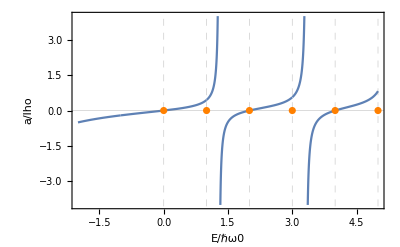

```mathematica
(*expression for a*)
aS[e_]:=-√(2π)/sF[-(e)/2,n];
(*isotropic case*)
aSISO[e_]:=aSISO[e]=(1/2)(Gamma[1/4-e/2-3/4]/Gamma[3/4-e/2-3/4]); 

n=6;
lho=√(ℏ/(μ ωz));
Show[{
Plot[{aS[e]},{e,-2,5},Axes->False,Frame->True,FrameLabel->{"E/ℏω0","a/lho"},GridLines->{{#,Dashed}&/@Range[0,5,1],{0}},PlotRange->{All,{-4,4}},LabelStyle->{Black,17}],
ListPlot[{#,0}&/@Range[0,5],PlotStyle->Orange]
}]
```

```mathematica
as=-1650a0;513a0;219.607 a0;-1000a0;
at=33a0;247.462 a0;
aUp=at;
aDown=0.4375as+0.5625at; (*flip Cs*)

eUp=e/.Solve[aS[e]==aUp/lho&&-2<e&&e<1.3,e][[1]];
eDown=e/.Solve[aS[e]==aDown/lho&&-2<e&&e<1.3,e][[1]];

a=(eUp) ωz /2/π
b=(eDown) ωz/2/π
d=(eUp-eDown)ωz/2/π
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1438.95

-30812.5

32251.5

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

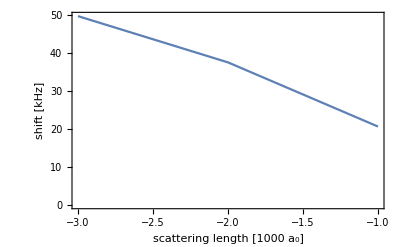

```mathematica
dat=Reap[
Do[
at=33a0;247.462 a0;
aUp=at;
aDown=0.4375as+0.5625at; (*flip Cs*)

eUp=e/.Solve[aS[e]==aUp/lho&&-2<e&&e<1.3,e][[1]];
eDown=e/.Solve[aS[e]==aDown/lho&&-2<e&&e<1.3,e][[1]];

a=(eUp) ωz /2/π;
b=(eDown) ωz/2/π;
d=(eUp-eDown)ωz/2/π;
Sow[{as/a0,a,b,d}]
,{as,0,-10000a0,-1000a0}]
][[2,1]];

ListPlot[dat[[2;;,{1,4}]]/1000,Joined->True,Axes->False,Frame->True,FrameLabel->{"scattering length [1000 a_0]","shift [kHz]"},LabelStyle->{Black,17}]
```